Piecewise[{{{1}, t==0}, {{ⅇ^-t}, 0<t≤1}, {{ⅇ^(-2+t)}, 1<t≤2}, {0, True}}]

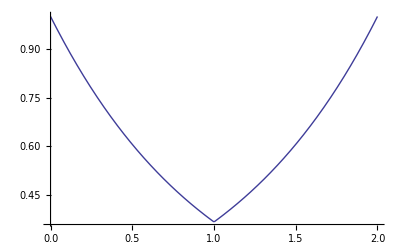

```mathematica
ClearAll;
s1:=DSolve[{x'[t]+x[t]==0,x[0]==1},x[t],t];
y1[t_]:=Evaluate[x[t]/.s1];
s2:=DSolve[{x'[t]-x[t]==0,x[1]==Evaluate[y1[1]]},x[t],t];
y2[t_]:=Evaluate[x[t]/.s2];
y:=Piecewise[{{y1[0],t==0},{y1[t],0<t≤1},{y2[t],1<t≤2}}]
y
Plot[y,{t,0,2},PlotRange->All]
```